#### Illustrate a problematic elastic map for the built-in Mathematica function NMinimize INSTRUCTIONS: Run common_funs.nb, ES_FindSymGroups.nb, chooseTmat.nb, then this notebook

```mathematica
Tmat = TmatBrown;
```

#### The problematic point is the closest MONO to closestMONO (dt = 0.5). By definition, the closest MONO to closestMONO should have beta = 0, but it does not. This impacts the trajectory from MONO to ORTH as well.

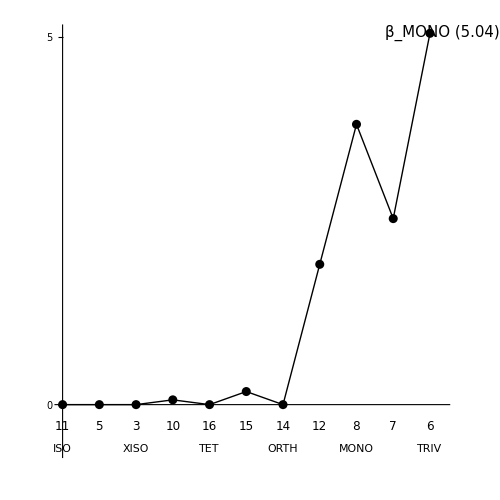

#### Define a function to minimize a square patch. Adjust dθ based on how close the local minima are.

```mathematica
dtheta = 0.2π;
dphi=dtheta;
```

```mathematica
Flocal[theta0_,phi0_,dtheta_,dphi_,Tmat_]:=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],theta0-dtheta≤θ≤theta0+dtheta&&phi0-dphi≤ϕ≤phi0+dphi},{θ,ϕ},Method->"RandomSearch"]
```

#### The original GetTempAndθ0σ0ϕ0 from ES_FindSymGroups.nb

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],0.05≤θ≤π+0.05&&0≤ϕ≤π},{θ,ϕ},Method->"RandomSearch"];
θ0=θ/.temp[Tmat,MONO][[2,1]];
σ0=0;
ϕ0=ϕ/.temp[Tmat,MONO][[2,2]];)
```

#### Closest MONO map to the input TRIV map:

```mathematica
WantDetails="WantDetails";
OutputFor[Tmat,MONO]
```

#### CORRECT MINIMUM: Upper left blue patch (green point) and its antipode region:

```mathematica
Flocal[0.5π,0.75π,dtheta,dphi,Tmat]
Flocal[1.5π,0.3π,dtheta,dphi,Tmat]
```

#### Central blue patch and its antipode region:

```mathematica
Flocal[π,0.5π,dtheta,dphi,Tmat]
Flocal[0.,0.5π,dtheta,dphi,Tmat]
```

#### Lower left blue patch and its antipode region:

```mathematica
Flocal[0.4 π,0.2π,dtheta,dphi,Tmat]
Flocal[1.4π,0.8π,dtheta,dphi,Tmat]
```

#### The full search finds the right minimum (as before):

```mathematica
Flocal[π,0.5π,π,0.5π,Tmat]
```

#### Now we start with the MONO map closest to our initial map. Same as the 6x6 matrix above:

```mathematica
TmatMONO=Closest[Tmat,MONO];
MatrixForm[TmatMONO]
```

#### With the original GetTempAndθ0σ0ϕ0. Mathematica gets the wrong min.

```mathematica
OutputFor[TmatMONO,MONO]
```

```mathematica
βT[TmatMONO,MONO]/Degree
```

#### CORRECT MINIMUM: Upper left blue patch and its antipode region:

```mathematica
Flocal[0.5π,0.75π,dtheta,dphi,TmatMONO]
Flocal[1.5π,0.3π,dtheta,dphi,TmatMONO]
```

#### INCORRECT MINIMUM: Central blue patch and its antipode region:

```mathematica
Flocal[π,0.5π,dtheta,dphi,TmatMONO]
Flocal[0.,0.5π,dtheta,dphi,TmatMONO]
```

#### LOCAL MINIMUM: Lower left blue patch (green dot) and its antipode region:

```mathematica
Flocal[0.4 π,0.2π,dtheta,dphi,TmatMONO]
Flocal[1.4π,0.8π,dtheta,dphi,TmatMONO]
```

#### By extending the θ search range slightly, it finds the correct minimum:

```mathematica
fac=1.15; (* NMinimize fails *)
fac=1.2; (* NMinimize works *)
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],0.05≤θ≤fac π+0.05&&0≤ϕ≤π},{θ,ϕ},Method->"RandomSearch"];
θ0=θ/.temp[Tmat,MONO][[2,1]];
σ0=0;
ϕ0=ϕ/.temp[Tmat,MONO][[2,2]];)
OutputFor[TmatMONO,MONO]
```